# Analysing Data

## Import data

### Import

```mathematica
$Path
```

{C:\Users\erik_\eclipse\plugins\com.wolfram.eclipse.MEET_10.1.1087\MathematicaSourceVersioned\Head,C:\Users\erik_\eclipse\plugins\com.wolfram.eclipse.MEET_10.1.1087\MathematicaSource,C:\Users\erik_\eclipse\configuration\org.eclipse.osgi\445\0\.cp\MathematicaSource,C:/Users/erik_/Documents/erik documents/PUCP/Maestria-Fisica/Ciclo-2/Fisica_Computacional/WorkSpaces/CompPhys3,C:\Users\erik_\AppData\Roaming\Mathematica\DocumentationIndices,C:\Program Files\Wolfram Research\Mathematica\12.3\SystemFiles\Links,C:\Users\erik_\AppData\Roaming\Mathematica\Kernel,C:\Users\erik_\AppData\Roaming\Mathematica\Autoload,C:\Users\erik_\AppData\Roaming\Mathematica\Applications,C:\ProgramData\Mathematica\Kernel,C:\ProgramData\Mathematica\Autoload,C:\ProgramData\Mathematica\Applications,.,C:\Users\erik_,C:\Program Files\Wolfram Research\Mathematica\12.3\AddOns\Packages,C:\Program Files\Wolfram Research\Mathematica\12.3\SystemFiles\Autoload,C:\Program Files\Wolfram Research\Mathematica\12.3\AddOns\Autoload,C:\Program Files\Wolfram Research\Mathematica\12.3\AddOns\Applications,C:\Program Files\Wolfram Research\Mathematica\12.3\AddOns\ExtraPackages,C:\Program Files\Wolfram Research\Mathematica\12.3\SystemFiles\Kernel\Packages,C:\Program Files\Wolfram Research\Mathematica\12.3\Documentation\English\System,C:\Program Files\Wolfram Research\Mathematica\12.3\SystemFiles\Data\ICC}

```mathematica
Import["Data/crust.dat"]
```

{{0.,2.4},{5.,2.4808},{10.,2.5617},{15.,2.6425},{20.,2.7233},{25.,2.8042},{30.,2.885},{35.,2.9658}}

```mathematica
Import["Data/innerCore.txt"]
```

5150.0000	12.1968
5260.0000	13.1173
5370.0000	13.1354
5480.0000	13.1535
5590.0000	13.1715
5700.0000	13.1896
5810.0000	13.2077
5920.0000	13.2258
6030.0000	13.2439
6140.0000	13.2620
6250.0000	13.2801
6360.0000	13.2982

```mathematica
Import["Data/innerCore.txt",{"Table","Data"}]
```

{{5150.,12.1968},{5260.,13.1173},{5370.,13.1354},{5480.,13.1535},{5590.,13.1715},{5700.,13.1896},{5810.,13.2077},{5920.,13.2258},{6030.,13.2439},{6140.,13.262},{6250.,13.2801},{6360.,13.2982}}

### importDATFile

```mathematica
?importDATFile
```

```mathematica
file=File["Data/innerCore.txt"]
```

File[Data/innerCore.txt]

```mathematica
importDATFile[file]
```

Dimensions:   xx122

{{5150.,12.1968},{5260.,13.1173},{5370.,13.1354},{5480.,13.1535},{5590.,13.1715},{5700.,13.1896},{5810.,13.2077},{5920.,13.2258},{6030.,13.2439},{6140.,13.262},{6250.,13.2801},{6360.,13.2982}}

```mathematica
importDATFile[file,HeaderLines->1]
```

Dimensions:   xx112

{{5260.,13.1173},{5370.,13.1354},{5480.,13.1535},{5590.,13.1715},{5700.,13.1896},{5810.,13.2077},{5920.,13.2258},{6030.,13.2439},{6140.,13.262},{6250.,13.2801},{6360.,13.2982}}

```mathematica
importDATFile[file,HeaderLines->1,"Rows"->All,"Transposed"->True]
```

Dimensions:   xx211

{{5260.,5370.,5480.,5590.,5700.,5810.,5920.,6030.,6140.,6250.,6360.},{13.1173,13.1354,13.1535,13.1715,13.1896,13.2077,13.2258,13.2439,13.262,13.2801,13.2982}}

## Data Interpolation

```mathematica
?interpolateDATFile
```

```mathematica
file=File["Data/upperMantle.dat"]
```

File[Data/upperMantle.dat]

```mathematica
idat=interpolateDATFile[file]
```

Dimensions:   xx262

<|InterpolatedFunction→InterpolatingFunction[…],Data→{{35.,2.9658},{60.,3.37},{85.,3.3728},{110.,3.3756},{135.,3.3783},{160.,3.387},{185.,3.4045},{210.,3.422},{235.,3.4395},{260.,3.457},{285.,3.4745},{310.,3.492},{335.,3.5095},{360.,3.542},{385.,3.597},{410.,3.652},{435.,3.707},{460.,3.762},{485.,3.817},{510.,3.865},{535.,3.9025},{560.,3.94},{585.,3.9775},{610.,4.015},{635.,4.0525},{660.,4.09}},Statistics→<|Mean→3.61415|>|>

```mathematica
idat["InterpolatedFunction"]
```

InterpolatingFunction[…]

```mathematica
idat["Data"]//Short
```

{{35.,2.9658},{60.,3.37},«23»,{660.,4.09}}

```mathematica
idat["Statistics"]
```

<|Mean→3.61415|>

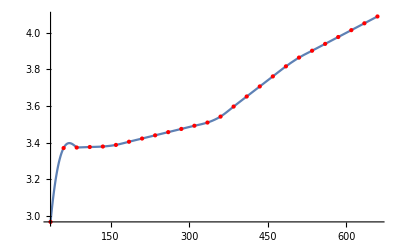

```mathematica
Plot[idat["InterpolatedFunction"][x],{x,35,660},
Epilog->{Red,Point[RandomSample[idat["Data"],26]]}]
```